```mathematica
y[x_]:=1-x+Sum[2*(-1+1-(-1)^n)/(Pi*n*(1-(n*Pi)^2))*Sin[n*Pi*x],{n,1000}]
```

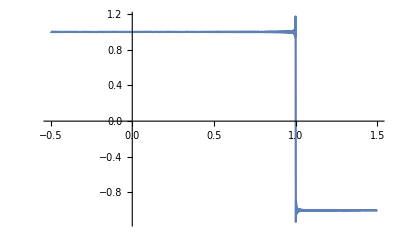

```mathematica
Plot[y''[x]+y[x],{x,-0.5,1.5}]
```

```mathematica
y2[x_]:=Sum[2*((1-(-1)^n)/(Pi*n)-n*Pi)/(1-(Pi*n)^2)*Sin[n*Pi*x],{n,100}]
```

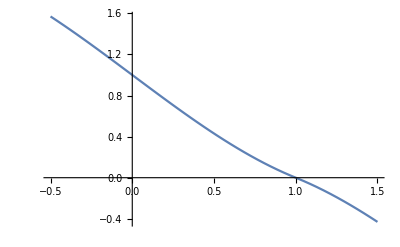

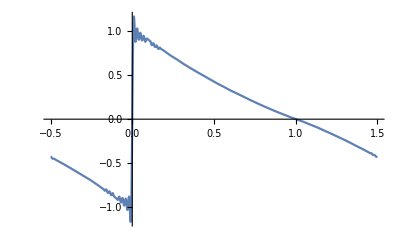

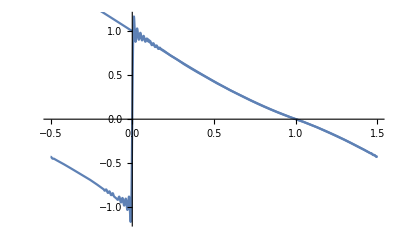

```mathematica
Plot[y[x],{x,-0.5,1.5}]
Plot[y2[x],{x,-0.5,1.5}]
Show[Plot[y2[x],{x,-0.5,1.5}],Plot[y[x],{x,-0.5,1.5}]]
```

```mathematica
sol3c[x_]:=(4*x^-1-4*x^-2)*Integrate[(xp^3/4-xp^2/2)*xp,{xp,x,2}]+(2*x^-2-x^-1)*Integrate[(xp^2-xp^3)*xp,{xp,1,x}]
```

```mathematica
sol3c[x_]:=(-102+54*x-x^5)/(20*x^2);
```

```mathematica
test3c[x_]:=sol3c''[x]+4*sol3c'[x]/x+2 sol3c[x]/x^2
test3c[1.2]
test3c[1.5]
test3c[1.8]
```

1.2

1.5

1.8

```mathematica
Simplify@sol3c[x]
```

(30-31 x+x^5)/(20 x^2)